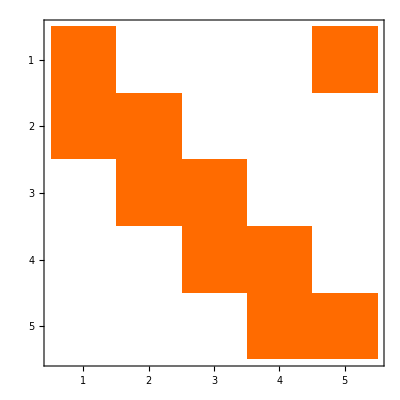

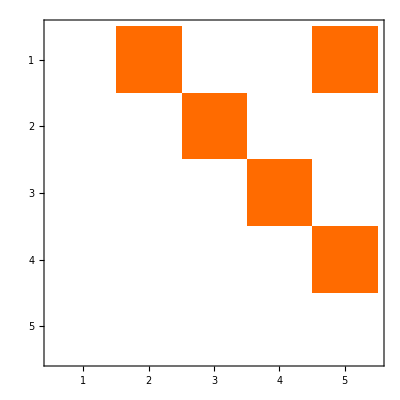

```mathematica
S = 32;
B1 = ConstantArray[0,{S,S}];
Do[
If[x2==x1-1||x2==x1||(x1==1 &&x2==S),
B1[[x1,x2]]=1,Nothing],{x2,1,S},{x1,1,S}];

B2 = ConstantArray[0,{S,S}];
Do[
If[x2==x1+1||(x1==1 &&x2==S),
B2[[x1,x2]]=1,Nothing],{x2,1,S},{x1,1,S}];

TMax=64;
res = ArrayFlatten[Table[If[t1==t2,B2,If[t1==t2-1,B1,If[t1==TMax&&t2==1,B1,0]]],{t1,1,TMax},{t2,1,TMax}]];
GraphPlot3D[res+Transpose[res]]
```

-Graphics3D-